```mathematica
SetDirectory["~/Code/mesons/data"];
Needs["PlotLegends`"];
```

```mathematica
bPoints=Import["bottom_points.csv"];
cPoints=Import["charm_points.csv"];

bLine=Fit[bPoints,{1,x},x]
```

9.01124+0.230043 x

```mathematica
cLine=Fit[cPoints,{1,x},x]
```

2.42771+0.296892 x

```mathematica
(* These are manually extrapolated points using cLine and bLine and the numerically found roots. *)
cExtrapolated = {{6.7867080898,4.442629},{7.9441335869,4.786259709},{9.0226508531,5.106462857}};
bExtrapolated={{10.0401743414,11.320911826},{11.0085243036,11.543673956},{11.9360155631,11.757036828}};
```

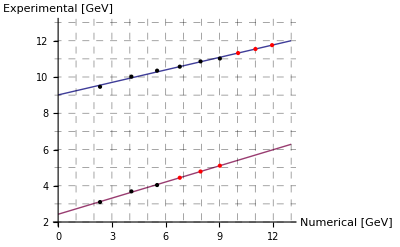

```mathematica
Plot[
{bLine,cLine},{x,0,13},
PlotRange->{{0,13.01},{2,13.01}},
GridLines->{Range[13],Range[13]},
GridLinesStyle->Directive[Black,Opacity[0.5],Dashed],
Epilog->{
{
PointSize[Medium],
Point[bPoints],
Point[cPoints]
},
{
PointSize[Large],
Red,
Point[cExtrapolated],
Point[bExtrapolated]
}
},
AxesLabel->{"Numerical\n[GeV]","Experimental\n[GeV]"},
PlotLegend->{"Bottom","Charm"},
LegendPosition->{0.8,0},
LegendShadow->None,
LegendTextSpace->10,
LegendBorder->None
]
```

```mathematica
airyOne=Import["airy_one.csv"];
airyTwo=Import["airy_two.csv"];
airyThree=Import["airy_three.csv"];
```

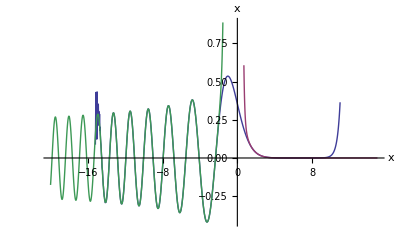

```mathematica
ListLinePlot[
{airyOne,airyTwo,airyThree},
(* Don't use that crappy yellow *)
PlotStyle->{ColorData[1,1],ColorData[1,2],ColorData[1,4]},
AxesLabel->{Style[x,13],Style[AiryAi[x],13]},
PlotLegend->{Style["First",13],Style["Second",13],Style["Third",13]},
LegendPosition->{0.6,0.2},
LegendShadow->None,
LegendBorder->None,
LegendTextSpace->8
]
```